```mathematica
(*ClearAll["Global`*"]*)
```

```mathematica
Needs["CUDALink`"]
```

Step 1

```mathematica
r=√(x^2+y^2+z^2);
G=1/(4 Pi k)*  1/r;
IntG=Simplify[Integrate[G/.{x->x-ξ},ξ]];
DIntG=Simplify[(IntG/.{ξ->a})-(IntG/.{ξ->-a})]
DIntGF[x_,y_,z_,a_]=(-Log[-a+x+√((a-x)^2+y^2+z^2)]+Log[a+x+√((a+x)^2+y^2+z^2)])/(4 k π)
IntG2=Integrate[DIntG/.{y->y-ξ1},ξ1]
DIntG3[x_,y_,z_,a_,b_]=Simplify[(IntG2/.{ξ1->b})-(IntG2/.{ξ1->-b})]
k=1;
ContourPlot[DIntG3[x,y,1,1,1],{x,-2.5,2.5},{y,-2.5,2.5},ColorFunction->(Hue[1-#]&),Contours->40,ContourLabels->All];(* Распределение потенциала для точеного приложения нагрузки*)
```

(Log[1+(a-x)/(√((a-x)^2+y^2+z^2))]-Log[1+(-a+x)/(√((a-x)^2+y^2+z^2))]-Log[1+(-a-x)/(√((a+x)^2+y^2+z^2))]+Log[1+(a+x)/(√((a+x)^2+y^2+z^2))])/(8 k π)

(-Log[-a+x+√((a-x)^2+y^2+z^2)]+Log[a+x+√((a+x)^2+y^2+z^2)])/(4 k π)

1/(8 k π)(((a z^2-x z^2) ArcTan[((a-x) (y-ξ1))/(z √(a^2-2 a x+x^2+z^2+(y-ξ1)^2))])/((a-x) z)-((-a z^2+x z^2) ArcTan[((a-x) (y-ξ1))/(z √(a^2-2 a x+x^2+z^2+(y-ξ1)^2))])/((a-x) z)-((-a z^2-x z^2) ArcTan[((a+x) (y-ξ1))/(z √(a^2+2 a x+x^2+z^2+(y-ξ1)^2))])/((a+x) z)+((a z^2+x z^2) ArcTan[((a+x) (y-ξ1))/(z √(a^2+2 a x+x^2+z^2+(y-ξ1)^2))])/((a+x) z)-(y-ξ1) Log[1+(a-x)/(√(a^2-2 a x+x^2+z^2+(y-ξ1)^2))]+(y-ξ1) Log[1+(-a+x)/(√(a^2-2 a x+x^2+z^2+(y-ξ1)^2))]+(y-ξ1) Log[1+(-a-x)/(√(a^2+2 a x+x^2+z^2+(y-ξ1)^2))]-(y-ξ1) Log[1+(a+x)/(√(a^2+2 a x+x^2+z^2+(y-ξ1)^2))]-(a-x) Log[y+√(a^2-2 a x+x^2+z^2+(y-ξ1)^2)-ξ1]+(-a+x) Log[y+√(a^2-2 a x+x^2+z^2+(y-ξ1)^2)-ξ1]+(-a-x) Log[y+√(a^2+2 a x+x^2+z^2+(y-ξ1)^2)-ξ1]-(a+x) Log[y+√(a^2+2 a x+x^2+z^2+(y-ξ1)^2)-ξ1])

1/(8 k π)(2 z ArcTan[((a-x) (-b+y))/(z √(a^2-2 a x+x^2+(b-y)^2+z^2))]+2 z ArcTan[((a+x) (-b+y))/(z √(a^2+2 a x+x^2+(b-y)^2+z^2))]-2 z ArcTan[((a-x) (b+y))/(z √(a^2-2 a x+x^2+(b+y)^2+z^2))]-2 z ArcTan[((a+x) (b+y))/(z √(a^2+2 a x+x^2+(b+y)^2+z^2))]+b Log[1+(a-x)/(√(a^2-2 a x+x^2+(b-y)^2+z^2))]-y Log[1+(a-x)/(√(a^2-2 a x+x^2+(b-y)^2+z^2))]-b Log[1+(-a+x)/(√(a^2-2 a x+x^2+(b-y)^2+z^2))]+y Log[1+(-a+x)/(√(a^2-2 a x+x^2+(b-y)^2+z^2))]-2 a Log[-b+y+√(a^2-2 a x+x^2+(b-y)^2+z^2)]+2 x Log[-b+y+√(a^2-2 a x+x^2+(b-y)^2+z^2)]-b Log[1+(-a-x)/(√(a^2+2 a x+x^2+(b-y)^2+z^2))]+y Log[1+(-a-x)/(√(a^2+2 a x+x^2+(b-y)^2+z^2))]+b Log[1+(a+x)/(√(a^2+2 a x+x^2+(b-y)^2+z^2))]-y Log[1+(a+x)/(√(a^2+2 a x+x^2+(b-y)^2+z^2))]-2 a Log[-b+y+√(a^2+2 a x+x^2+(b-y)^2+z^2)]-2 x Log[-b+y+√(a^2+2 a x+x^2+(b-y)^2+z^2)]+b Log[1+(a-x)/(√(a^2-2 a x+x^2+(b+y)^2+z^2))]+y Log[1+(a-x)/(√(a^2-2 a x+x^2+(b+y)^2+z^2))]-b Log[1+(-a+x)/(√(a^2-2 a x+x^2+(b+y)^2+z^2))]-y Log[1+(-a+x)/(√(a^2-2 a x+x^2+(b+y)^2+z^2))]+2 a Log[b+y+√(a^2-2 a x+x^2+(b+y)^2+z^2)]-2 x Log[b+y+√(a^2-2 a x+x^2+(b+y)^2+z^2)]-b Log[1+(-a-x)/(√(a^2+2 a x+x^2+(b+y)^2+z^2))]-y Log[1+(-a-x)/(√(a^2+2 a x+x^2+(b+y)^2+z^2))]+b Log[1+(a+x)/(√(a^2+2 a x+x^2+(b+y)^2+z^2))]+y Log[1+(a+x)/(√(a^2+2 a x+x^2+(b+y)^2+z^2))]+2 a Log[b+y+√(a^2+2 a x+x^2+(b+y)^2+z^2)]+2 x Log[b+y+√(a^2+2 a x+x^2+(b+y)^2+z^2)])

Step 2

```mathematica
fres[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,Re[p0 √(1-(x/a)^2-(y/b)^2)],0];
a=1;(*большая полуось эллипса*);
b=a/2;(*меньшая полуось эллипса*);
s=1.5*a;(*размер расчетной области*)
h= 3a /39;(*размер ГЭ*)
n=2 s/h+1(*number of elementary units*)
p0=1;
(*array of X-coordinates*)
X=Table[xh,{xh,-s,s,h}];
Y=Table[yh,{yh,-s,s,h}];
Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,Re[p0 √(1-(x/a)^2-(y/b)^2)],0];
```

40.

```mathematica
(*функция поверхностного распределенимя*)
Plot3D[Pressure[x,y,a,b,p0],{x,-s,s},{y,-s,s},AxesLabel->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
PressureTab=Table[Pressure[X[[xi]],Y[[yj]],a,b,p0]//N,{xi,1,n},{yj,1,n}];(*дискретизация функции поверхностного распределенимя*)
ListPlot3D[PressureTab,InterpolationOrder->0,Filling->Bottom,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
be=Table[{X[[xi]],Y[[yj]],PressureTab[[xi,yj]]},{xi,1,n},{yj,1,n}];
(*граничные элементы*)
```

Step 3

```mathematica
Pk1 = Table[Subscript[p, k],{k,1,n^2}];
PotV[xj_,yj_] =Table[DIntG3[X[[m]]-xj,Y[[o]]-yj,-0.001,h,h],{m,1,n},{o,1,n}];
FPT=Flatten[PressureTab];
```

```mathematica
(*AbsoluteTiming[InvertedMatrix=Get["B:\\wolf.doc's\\Курсовая 3 курс\\Цифры(\\InvertedMatrix20CUDA.txt"];];*)
```

```mathematica
AbsoluteTiming[A={};
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,A=Join[A,{Flatten[PotV[X[[i]],Y[[j]]]]},1];]]
]
InvertedMatrix = Inverse[A];
```

{20.4689,Null}

******************************************************************************************************************************************************************************************

```mathematica
Hold[AbsoluteTiming[InvertedMatrix={};
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,A=Join[A,{Flatten[PotV[X[[i]],Y[[j]]]]},1];]]
]];(*код для определения матрицы коэффициентов А, которая используется при решении СЛАУ матричным методом*)
```

```mathematica
Hold[AbsoluteTiming[Ainv=Inverse[A];Ainv>>"B:\\wolf.doc's\\Курсовая 3 курс\\Цифры(\\InvertedMatrix60CUDA.txt";]];(*При необходимости записываем матрицу,обратную матрице А в файл, так как считывать её из файла оптимальнее, чем получать каждый раз заново*)
```

```mathematica
Hold[Potq[xj_,yj_] = Sum[DIntG3[X[[m]]-xj,Y[[o]]-yj,-0.001,h,h]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}];
Equationq=Flatten[Table[Potq[X[[i]],Y[[j]]]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];
Solq = Solve[Equationq,Pk1];
SolNq=Table[Solq[[1,i,2]],{i,1,n*n}];];(*Не выполняем этот код, так как есть более оптимизированный*)
```

******************************************************************************************************************************************************************************************

```mathematica
cudaMemInvertedMatrix=CUDAMemoryLoad[InvertedMatrix];
cudaMemAppliedForce = CUDAMemoryLoad[FPT];
```

```mathematica
AbsoluteTiming[SearchForceWithCuda=CUDADot[cudaMemInvertedMatrix,cudaMemAppliedForce]];
```

```mathematica
AbsoluteTiming[PLS1=Dot[InvertedMatrix,FPT];];
```

```mathematica
SolN1q = Table[CUDAMemoryGet[SearchForceWithCuda][[n  i +j-n]],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Axis,Mesh->None]
```

-Graphics3D-

```mathematica
DIntG3Res=Function[{x,y,z},∑_(i=1)^n ∑_(j=1)^n DIntG3[X[[i]]-x,Y[[j]]-y,z,h,h]*SolN1q[[i,j]]];
```

```mathematica
AbsoluteTiming[Resq=Table[DIntG3Res[X[[i]],Y[[j]],-0.001],{i,1,n},{j,1,n}];];
```

```mathematica
ListPlot3D[Resq,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
SeqSet={{20,0.0098949},{40,0.134317},{60,0.799889},{80,3.5948636563}};
ParalelSet={{20,0.0015787},{40,0.0082962},{60,0.0214812},{80,0.0563654}};
```

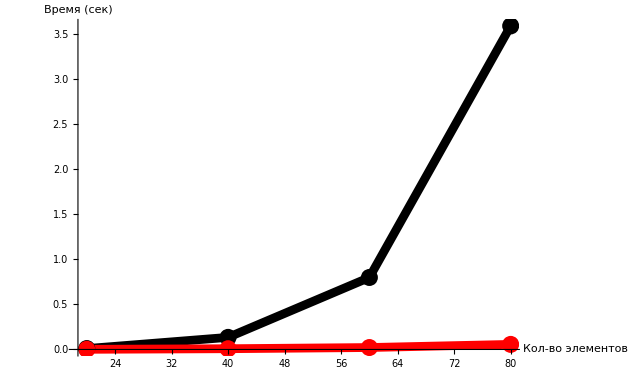

```mathematica
ListLinePlot[{SeqSet,ParalelSet,SeqSet,ParalelSet},
PlotRange->All,PlotStyle->{{Black,Thickness[0.01]},{Red,Thickness[0.01]}},
AxesLabel->{"Кол-во элементов","Время (сек)"},
LabelStyle->{FontFamily->"Times New Roman",20},
Joined->{True,True,False,False}]
```

```mathematica
BoostSet={{0,0},{20,6.267751947805157},{40,16.190183457486558},{60,37.2366999981379},{80,63.777843434}};
```

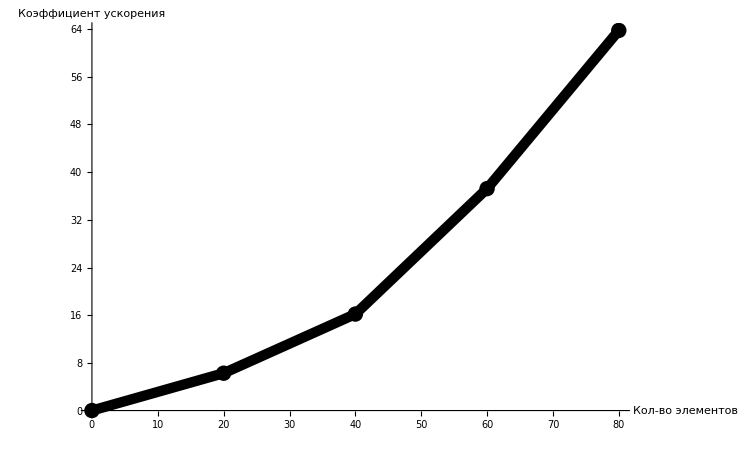

```mathematica
ListPlot[{BoostSet,BoostSet},
PlotRange->All,PlotStyle->{{Black,Thickness[0.01]},{Black,PointSize[0.015]}},
AxesLabel->{"Кол-во элементов","Коэффициент ускорения"},
LabelStyle->{FontFamily->"Times New Roman",20},
Joined->{True,False}]
```